```mathematica
y1 =x1^2+(2*x2+2*x3+2)*x1+2*x2^2+2*x2+2*x3^2+2*x3;
y2 = 2*x1-2*x3-2*x1*x2-2*x2*x3+3*x1^2+x3^2;
y3 = x1^2 + x2^2 + x3^2;

(* the proper way to define quadratic form
{x1, x2, x3}.A1.{x1,x2,x3}+b1.{x1,x2,x3} *)


 S = Solve[y1==Y1 && y2 ==Y2 && y3 == Y3 , {x1, x2, x3}]
```

{{x1→Root[32 Y1^2+8 Y1^3+5 Y1^4+64 Y1 Y2+32 Y1^2 Y2+24+(2688-736 Y1-248 Y1^2-2688 Y2+256 Y1 Y2+256 Y2^2+6112 Y3+480 Y1 Y3-1280 Y2 Y3+608 Y3^2) #1^3+(4512-808 Y1+94 Y1^2-2400 Y2+128 Y1 Y2+64 Y2^2+5624 Y3-648 Y1 Y3-448 Y2 Y3+1064 Y3^2) #1^4+(4368-824 Y1-960 Y2+2848 Y3) #1^5+(2616+44 Y1-96 Y2-144 Y3) #1^6+696 #1^7+261 #1^8&,1],x2→(351+1)/1,x3→(349+1377558 Y3^2 1^7)/(13167360+9210240 Y1+68+108160 Y3^5)},6,{x1→1,x2→1,x3→1}}
 |  |  |  |

```mathematica
(* Taking the solution, replacing root with List, taking the polynomial out *)
Poly:=((List @@ (x1/.S[[1]]))[[1]])
```

```mathematica
Quq=Discriminant[Poly[z], z]
```

18807032043899191296 (13134378933714217402368 Y1^2+74831326227576855724032 Y1^3+193333566202802360082432 Y1^4+301843711422119961538560 Y1^5+321531252513768427864320 Y1^6+251682405599505893596416 Y1^7+153541756463195685994560 Y1^8+76983770751520392381312 Y1^9+6117+1193398265704152268800 Y2 Y3^26+167410624396857753600 Y1 Y2 Y3^26+49113483008099328000 Y2^2 Y3^26-212904361939516416000 Y3^27-26108699177014272000 Y1 Y3^27-16256813966714880000 Y2 Y3^27+2473227593740800000 Y3^28)
 |  |  |  |

```mathematica
ContourPlot3D[Quq==0,{Y1,-5,35},{Y2,-10,40},{Y3,0,9}, Axes->True,AxesStyle->Directive[Black,30],MaxRecursion->4]
```

$Aborted

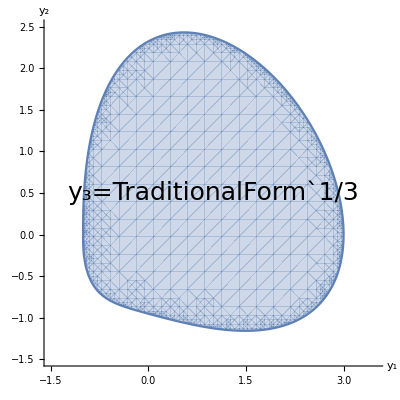

```mathematica
Y3sec =1/3;
Qplot = Quq/.{Y3 -> Y3sec};
poly2 = Factor[Qplot][[4]];
RegionPlot[poly2≤0,{Y1,-1.5,3.5},{Y2,-1.5,2.5},Axes->True,Frame->None,AxesStyle->Directive[Black,40],TicksStyle->Directive[Black, 20],AxesLabel->{Style["y_1",FontSize->22],Style["y_2",FontSize->22]}, MaxRecursion->4,Epilog->{Text[Style[StringForm["y_3=`1`",Y3sec],25],Scaled[{0.5,0.5}]]},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->20}]
```

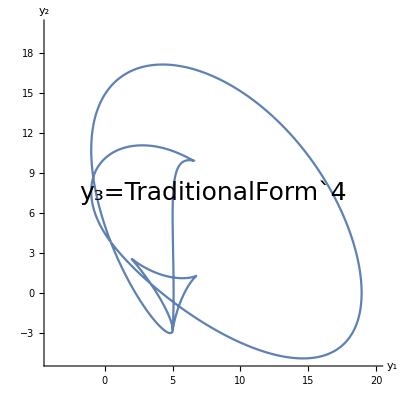

```mathematica
Y3sec =4;
Qplot = Quq/.{Y3 -> Y3sec};
poly2 = Factor[Qplot][[4]];
plot=ContourPlot[poly2==0,{Y1,-4,20},{Y2,-5,20},Axes->True,Frame->None,AxesStyle->Directive[Black,40],TicksStyle->Directive[Black, 20],AxesLabel->{Style["y_1",FontSize->22],Style["y_2",FontSize->22]}, MaxRecursion->4,Epilog->{Text[Style[StringForm["y_3=`1`",Y3sec],25],Scaled[{0.5,0.5}]]},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->20}]
```

```mathematica
points=Cases[Normal@plot,Line[pts_,___]:>pts,Infinity];
```

```mathematica
list=Flatten[points,1];
xdiff=-4;
ydiff=0;
pts=list+ConstantArray[{-xdiff,-ydiff},Length[list]];
```

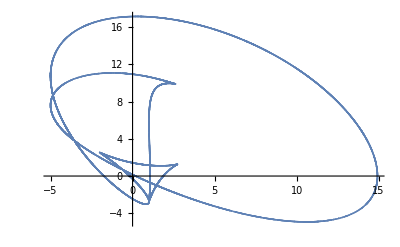

```mathematica
ListPlot[pts]
```

```mathematica
r=Norm/@pts
```

{15.6678,15.6684,15.6751,15.6817,15.6824,15.6824,15.6824,15.6892,15.6896,15.6901,15.6961,15.6969,15.6978,15.703,15.7042,15.7055,15.7099,15.7115,10928,2.91126,2.91673,2.90391,2.89507,2.90817,2.86519,2.86836,2.87797,2.89022,2.88387,2.88072,2.87013,2.86071,2.8499,2.84482,2.85248,2.86318,2.86519}
 |  |  |  |

```mathematica
phi=(ArcTan@@#1)&/@pts
```

{1.00125,1.00146,1.00367,1.00585,1.00608,1.00609,1.0061,1.00837,1.00851,1.00866,1.01066,1.01093,1.01122,1.01295,1.01335,1.01379,1.01523,10930,-1.22084,-1.21895,-1.21686,-1.2148,-1.21341,-1.21357,-1.21538,-1.21731,-1.21125,-1.21047,-1.20883,-1.20737,-1.20351,-1.20975,-1.21137,-1.2133,-1.21341}
 |  |  |  |

```mathematica
d=0.01
```

0.01

```mathematica
rad[alpha_]:=Max[MapThread[If[#1≤d,r[[#2]],0]&,{Abs[phi-alpha],Range[1,Length[phi]]}]]
(*rad[alpha_]:=Max[Nearest[phi->r,alpha,{1000,0.2}]]*)
```

```mathematica
(** too slow PolarPlot[rad[t],{t,0,Pi},PlotPoints->10,MaxRecursion->1] *)
```

```mathematica
rad[0.2]
```

14.9821

```mathematica
phis1=Range[-Pi,Pi,0.01];
```

```mathematica
rs1=rad/@phis1;
```

NearestFunction[{629, 1}, <>]

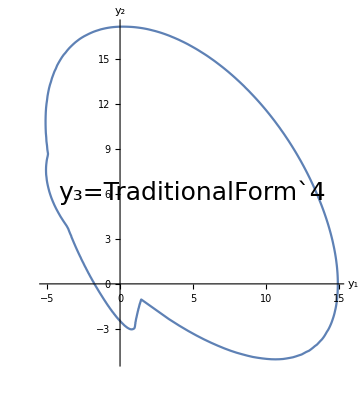

```mathematica
ListPolarPlot[Transpose[{phis1,rs1}],Joined->True,Axes->True,Frame->None,AxesStyle->Directive[Black,40],TicksStyle->Directive[Black, 20],AxesLabel->{Style["y_1",FontSize->22],Style["y_2",FontSize->22]}, Epilog->{Text[Style[StringForm["y_3=`1`",Y3sec],25],Scaled[{0.5,0.5}]]},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->20}]
```

```mathematica
Min[phi]
```

-3.14095

```mathematica
Flatten[Position[r,_?(#==0&)]]
```

```mathematica
Min[r]
```

0.115067

```mathematica
nf=Nearest[phis1->Automatic]
```

NearestFunction[{629, 1}, <>]

SetDelayed::write: Tag Integer in 1[x_] is Protected.

$Failed

```mathematica
IsInside[x_,y_]:=Norm[{x+xdiff,y+ydiff}]≤rs1[[nf[ArcTan[x+xdiff,y+ydiff]][[1]]]]
```

NearestFunction[{629, 1}, <>]

Nearest::dmtch: The dimension of {-3.14159, -3.13159, -3.12159, -3.11159, -3.10159, -3.09159, -3.08159, -3.07159, -3.06159, -3.05159, -3.04159, -3.03159, -3.02159, -3.01159, -3.00159, -2.99159, -2.98159, -2.97159, « 15 », -2.81159, -2.80159, -2.79159, -2.78159, -2.77159, -2.76159, -2.75159, -2.74159, -2.73159, -2.72159, -2.71159, -2.70159, -2.69159, -2.68159, -2.67159, -2.66159, -2.65159, « 579 »} and ArcTan[-4 + x, y] does not match.

Part::pkspec1: The expression ArcTan[-4 + x, y] cannot be used as a part specification.

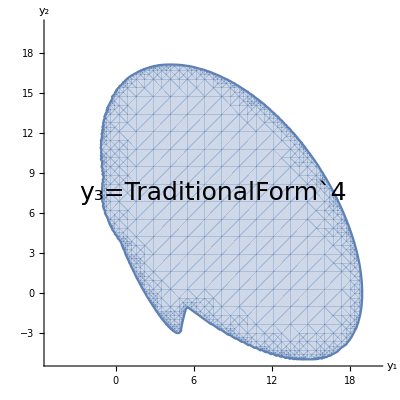

```mathematica
RegionPlot[IsInside[x,y],{x,-5,20},{y,-5,20},Axes->True,Frame->None,AxesStyle->Directive[Black,40],TicksStyle->Directive[Black, 20],AxesLabel->{Style["y_1",FontSize->22],Style["y_2",FontSize->22]}, MaxRecursion->4,Epilog->{Text[Style[StringForm["y_3=`1`",Y3sec],25],Scaled[{0.5,0.5}]]},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->20}]
```

```mathematica
IsInside[1,2]
```

False